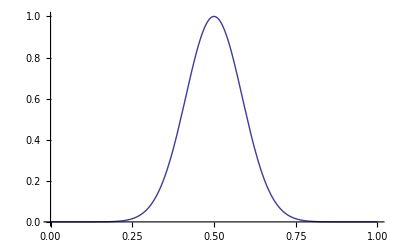

```mathematica
Gf[x_,α_,β_,γ_]=α Exp[(-(x-β)^2)/γ];
Plot[Gf[x,1,0.5,0.015],{x,0,1},PlotRange->All]
```

{{1-(-x+xR)/(-xL+xR),(-x+xR)/(-xL+xR)}}

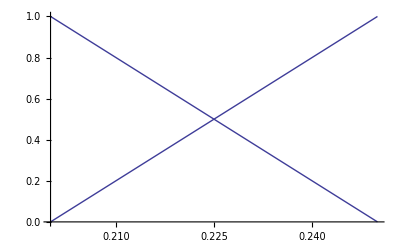

0.21708

```mathematica
x1=0.2;
x2=0.25;
ψ[x_,xL_,xR_]=({{1-(xR-x)/(xR-xL), (xR-x)/(xR-xL)}})
Plot[ψ[x,x1,x2],{x,x1,x2}]
Integrate[Gf[x,1,0.5,0.015],{x,0,1}]
```

```mathematica
RootApproximant[0.21708037468206032]
```

Root[1-3 #1-9 #1^2+9 #1^3-3 #1^4-20 #1^5-4 #1^6+8 #1^9+10 #1^10&,3]

{{y[x]→0.325621 (1.11421-3.99236×10^-9 ⅇ^((66.6667-66.6667 x) x)-0.614212 x-0.5 Erf[4.08248-8.16497 x]+1. x Erf[4.08248-8.16497 x])}}

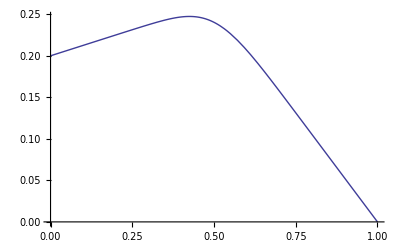

```mathematica
Kn=0.1;
sol = DSolve[{Kn^2/3 y''[x]==-Gf[x,0.01,0.5,0.015],y[0]==0.2,y[1]==0},y[x],x]
Plot[y[x]/.sol,{x,0,1}]
```